```mathematica
SetDirectory[NotebookDirectory[]];
```

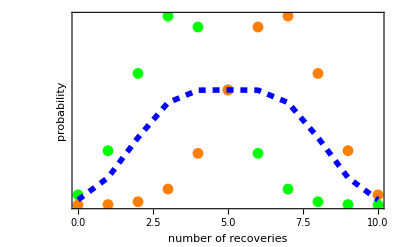

```mathematica
g1=DiscretePlot[{PDF[BinomialDistribution[10,0.35],x],PDF[BinomialDistribution[10,0.65],x],PDF[MixtureDistribution[{1,1},{BinomialDistribution[10,0.35],BinomialDistribution[10,0.65]}],x]},{x,0,10},PlotStyle->{Green,Orange,{Dashed,Blue,Thickness[0.01]}},Joined->{False,False,True},Filling->None,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"number of recoveries","probability"},BaseStyle->Medium]
```

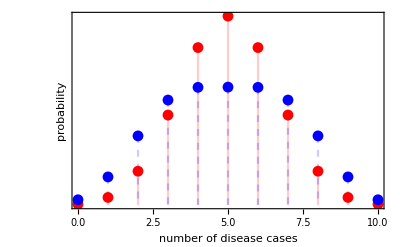

```mathematica
g2=DiscretePlot[{PDF[BinomialDistribution[10,0.5],x],PDF[MixtureDistribution[{1,1},{BinomialDistribution[10,0.35],BinomialDistribution[10,0.65]}],x]},{x,0,10},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"number of disease cases","probability"},BaseStyle->Medium,PlotStyle->{Red,{Blue,Dashed}}]
```

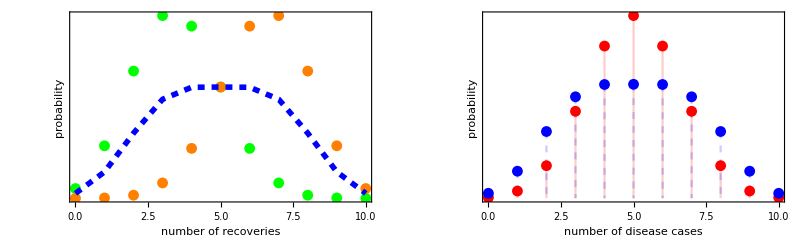

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_betaBinomialDispersion.pdf",gFinal]
```

Distributions_betaBinomialDispersion.pdf